## Setup

```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
DATADIR = FileNameJoin[ParentDirectory[], "/data/raw"] ;

CreateMatrix[nn_, mm_]:=Module[{J,vars,i},(*Variables du système*)
vars=Join[Table[H[i],{i,1,nn}],{H2},Table[P[i],{i,1,mm}],{P2}];

(*Initialiser la matrice jacobienne avec des zéros*)
J=ConstantArray[0,{nn+mm+2,nn+mm+2}];

(*Remplissage de la sous-matrice pour H[i]*)
Do[J[[i,i]]=-n mH-δH1-a P2[t];
If[i>1,J[[i,i-1]]=n mH],{i,1,nn}];
(*Remplissage des termes de parasitisme*)
Do[J[[i,nn+mm+2]]=-a*H[i][t],{i,1,nn}];
(*Termes liés à H2*)
J[[1,nn+1]]= r;
(*H1 dépend de H2*)
J[[nn+1,nn]]=n mH;
(*H2 dépend de H[k]*)
J[[nn+1,nn+1]]=-δH2;


(*Remplissage de la sous-matrice pour P[i]*)
Do[J[[nn+1+i,nn+1+i]]=-m mP-δP1;
If[i>1,J[[nn+1+i,nn+i]]=m mP],{i,1,mm}];
(*Remplissage des termes de parasitisme*)
Do[J[[nn+2,i]]=a  P2[t],{i,1,nn}];
J[[nn+2, nn+mm+2]] = a*H1[t];
(*Ligne de P2*)
J[[nn+mm+2,nn+mm+1]]=m mP;
J[[nn+mm+2,nn+mm+2]]=-δP2;

(*Retourner la matrice jacobienne*)
J];

VPdP2[X_?NumericQ,Y_?NumericQ]:=Module[
{eigs},
eigs=lJeq/.paramsplot/.{ρ->33,n->nn, m->mm}/.{δP2->1/tP2}/.{tH2->X, tP2->Y} //N// Eigenvalues;
If[Length[eigs]>=nn+mm+2,eigs[[nn+mm+2]] // Re,Indeterminate (*Return a safe fallback*)]
]

VPrho[X_?NumericQ,Y_?NumericQ]:=Module[
{eigs},
eigs=lJeq/.paramsplot/.{δP2 -> 8,n->nn, m->mm}/.{tH2->X, ρ->Y} //N// Eigenvalues;
If[Length[eigs]>=nn+mm+2,eigs[[nn+mm+2]] // Re,Indeterminate (*Return a safe fallback*)]
]

paramsplot = {mH->1,mP->2, δP1 -> 1, a-> 1, δH1 -> 0, δH2->1/tH2}
nmValues={{1,1},{2,1},{3,1},{5,1},{10,1},{20,1},{1,10},{2,10},{3,10},{5,10},{10,10},{20,10}}
```

{mH→1,mP→2,δP1→1,a→1,δH1→0,δH2→1/tH2}

{{1,1},{2,1},{3,1},{5,1},{10,1},{20,1},{1,10},{2,10},{3,10},{5,10},{10,10},{20,10}}

## Script tH2-ρ

```mathematica
paramInfo=StringJoin["mP_",ToString[mP/.paramsplot],
"_dP1_",ToString[δP1/.paramsplot],
"_dH1_",ToString[δH1/.paramsplot]];
Folder="Murdoch_stability_tH2-rho_"<>paramInfo;

CreateDirectory[Folder];

(*Storage for results*)
StabilityCurveData={};

(*Loop through parameter values*)
Monitor[
For[
i=1,i<=Length[nmValues],i++,Module[{currentN=nmValues[[i,1]],currentM=nmValues[[i,2]],sol,analysis},(*Set up the system with current n=m value*)
nn=currentN;
mm=currentM;

H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

θH = n*mH;
θP = m*mP;
r = ρ*δH2;
Clear[δH1]; (* On utilise les mortalités intrinsèques telles quelles*)
Clear[δP1];

lJ = CreateMatrix[nn,mm];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];
	
ρMin=2;ρMax=50; ρPas=0.5;
CourbeLimite = {};
For[rho=ρMin,rho<ρMax,rho+=ρPas,
tsol=tH2/. FindRoot[VPrho[tH2,rho],{tH2,.1,5},Method->"Brent"];
AppendTo[CourbeLimite,{tsol,rho}]
];

AppendTo[StabilityCurveData, CourbeLimite]
]


],{i,Length[nmValues]}
]
Export[FileNameJoin[{Folder,"nmRange.csv"}],nmValues];
Export[FileNameJoin[{Folder,"parameters.csv"}],paramsplot];
Export[FileNameJoin[{Folder,"data.csv"}],StabilityCurveData];
```

$Aborted

## C’est ρ qui a ces effets-là où le terme de reproduction r ? Fixons β plutôt que ρ pour investiguer ça

```mathematica
ClearAll;
nn=4;
mm=1;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

θH = n*mH;
θP = m*mP;
Clear[δH1]; (* On utilise les mortalités intrinsèques telles quelles*)
Clear[δP1];

lJ = CreateMatrix[nn,mm];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];

VPr[X_?NumericQ,Y_?NumericQ]:=Module[
{eigs},
eigs=lJeq/.paramsplot/.{δP2 -> 8,n->nn, m->mm}/.{tH2->X, r->Y} //N// Eigenvalues;
If[Length[eigs]>=nn+mm+2,eigs[[nn+mm+2]] // Re,Indeterminate (*Return a safe fallback*)]
]
	
rMin=2;rMax=100; rPas=0.5;
CourbeLimite = {};
For[ri=rMin,ri<rMax,ri+=rPas,
tsol=tH2/. FindRoot[VPr[tH2,ri],{tH2,.1,5},Method->"Brent"];
AppendTo[CourbeLimite,{tsol,ri}]
];
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {tH2} = {0.1}.

ReplaceAll::reps: {FindRoot[VPr[tH2,ri],{tH2,0.1,5},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {tH2} = {0.1}.

ReplaceAll::reps: {FindRoot[VPr[tH2,ri],{tH2,0.1,5},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {tH2} = {0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[VPr[tH2,ri],{tH2,0.1,5},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

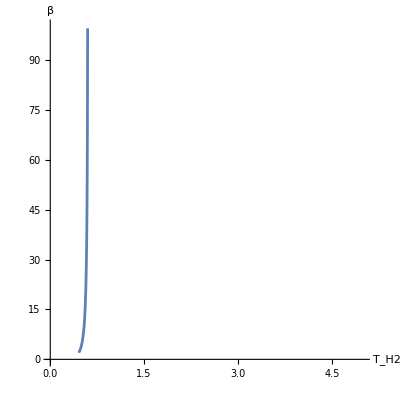

```mathematica
ListLinePlot[{CourbeLimite},
Axes->True,
AxesLabel -> {"T_H2", "β"},
PlotRange->{{0,5},{0,100}},
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1]
```

## changer n,m

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {tH2} = {0.1}.

ReplaceAll::reps: {FindRoot[VPr[tH2,ri],{tH2,0.1,5},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {tH2} = {0.1}.

ReplaceAll::reps: {FindRoot[VPr[tH2,ri],{tH2,0.1,5},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {tH2} = {0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[VPr[tH2,ri],{tH2,0.1,5},Method→Brent]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

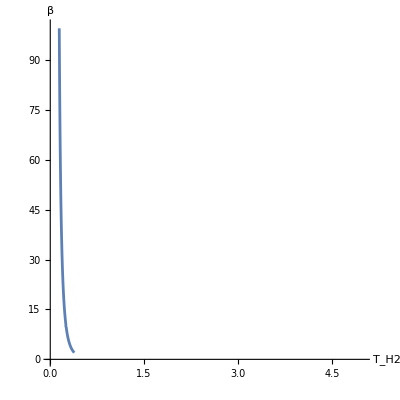

```mathematica
ClearAll;
nn=1;
mm=1;
H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

θH = n*mH;
θP = m*mP;
Clear[δH1]; (* On utilise les mortalités intrinsèques telles quelles*)
Clear[δP1];

lJ = CreateMatrix[nn,mm];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];

VPr[X_?NumericQ,Y_?NumericQ]:=Module[
{eigs},
eigs=lJeq/.paramsplot/.{δP2 -> 8,n->nn, m->mm}/.{tH2->X, r->Y} //N// Eigenvalues;
If[Length[eigs]>=nn+mm+2,eigs[[nn+mm+2]] // Re,Indeterminate (*Return a safe fallback*)]
]
	
rMin=2;rMax=100; rPas=0.5;
CourbeLimite = {};
For[ri=rMin,ri<rMax,ri+=rPas,
tsol=tH2/. FindRoot[VPr[tH2,ri],{tH2,.1,5},Method->"Brent"];
AppendTo[CourbeLimite,{tsol,ri}]
];

ListLinePlot[{CourbeLimite},
Axes->True,
AxesLabel -> {"T_H2", "β"},
PlotRange->{{0,5},{0,100}},
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1]
```

-> C’est bien l’effet du taux de fécondité lui-même β et non de tH2 dans ρ = tH2*β

## Graphes tH2-tP2

```mathematica
paramInfo=StringJoin["mP_",ToString[mP/.paramsplot],
"_dP1_",ToString[δP1/.paramsplot],
"_dH1_",ToString[δH1/.paramsplot]];
Folder="Murdoch_stability_tH2-dP2_"<>paramInfo;

CreateDirectory[Folder];

(*Storage for results*)
StabilityCurveData={};

(*Loop through parameter values*)
Monitor[
For[
i=1,i<=Length[nmValues],i++,Module[{currentN=nmValues[[i,1]],currentM=nmValues[[i,2]]},(*Set up the system with current n=m value*)
nn=currentN;
mm=currentM;

H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

lJ = CreateMatrix[nn,mm];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];

θH = n*mH;
θP = m*mP;
r = ρ*δH2;
Clear[δH1]; (* On utilise les mortalités intrinsèques telles quelles*)
Clear[δP1];

τ2Min=0.01;
τ2Max=1;
τ2Pas=0.02;

CourbeLimite={};
tP2Min=0.01;tP2Max=5;tP2Pas=0.05;
For[tP2=tP2Min,tP2<tP2Max,tP2+=tP2Pas,

tsol=tH2/. FindRoot[VPdP2[tH2,tP2],{tH2,0.01,10},Method->"Brent"];
AppendTo[CourbeLimite,{tsol,tP2}]
];

AppendTo[StabilityCurveData, CourbeLimite]
]


],{i,Length[nmValues]}
]
Export[FileNameJoin[{Folder,"nmRange.csv"}],nmValues];
Export[FileNameJoin[{Folder,"parameters.csv"}],paramsplot];
Export[FileNameJoin[{Folder,"data.csv"}],StabilityCurveData];
```